```mathematica
Plot[x^2,{x,-1,1}, AxesLebel -> {"X","Y"},PlotStyle -> {purple}, GridLines-> {{-1,-0.5,.5,1},{.2,.4,.6,.81}}]
```

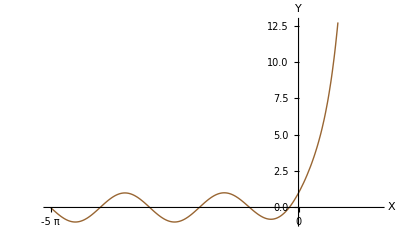

```mathematica
Plot[E^x+Sin[x],{x,-5π,5},AxesLabel-> {"X","Y"},PlotStyle->{Brown},
Ticks->{{-5π,-4π,3Pi,-Pi,0,Pi,2Pi,3Pi},Automatic}]
```

```mathematica
<<"PlotLegends`"
```

```mathematica
Plot[{Sin[x],Cos[x]},{x,-3Pi/2, 3Pi}, PlotStyle-> {Red,Green}, AxesLabel -> {"X","Y"}, PlotLegend -> {"Sin X", "Cos X"},LegendPosition-> {0.5,-0.8}]
```

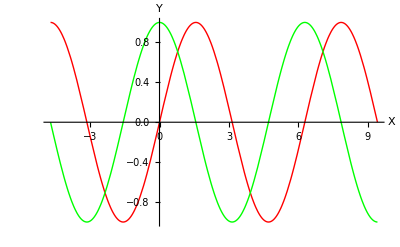

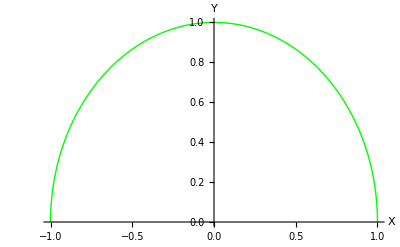

```mathematica
a = Plot[√(1-x^2),{x,-1,1}, AxesLabel -> {"X","Y"}, PlotStyle -> {Green}, PlotLegend -> {"√(1-x^2)"},LegendPosition-> {0.5,-0.5}]
```

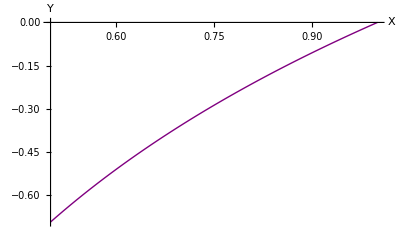

```mathematica
b =Plot[Log[x],{x,0.5,1}, AxesLabel -> {"X","Y"}, PlotStyle -> {Purple},PlotLegend -> {"Log[x]"},LegendPosition-> {0.5,-1}]
```

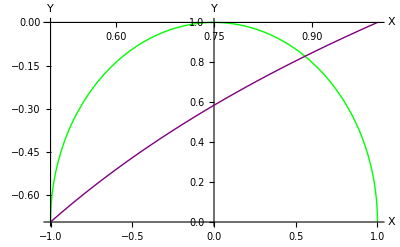

```mathematica
Show[a,b]
```

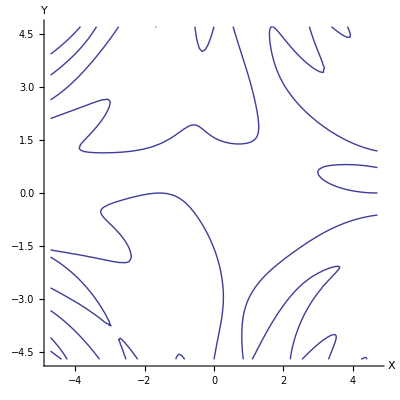

```mathematica
ContourPlot[Sin[x*y]== Sin[x]+Cos[y],{x,-3Pi/2, 3Pi/2},{y,-3Pi/2, 3Pi/2 }, AxesLabel-> {"X","Y"}, Axes -> True, Frame -> False]
```

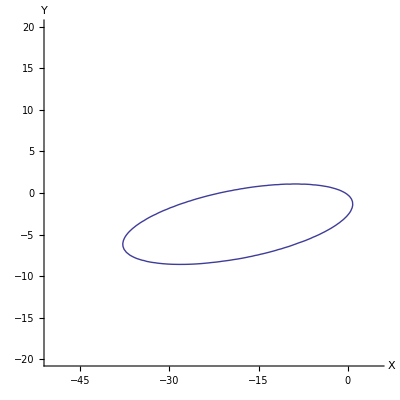

```mathematica
ContourPlot[x^2+16y^2-4x*y+22x+46y+9 == 0,{x,-50,5},{y,-20,20}, AxesLabel -> {"X","Y"}, Axes -> True, Frame -> False]
```

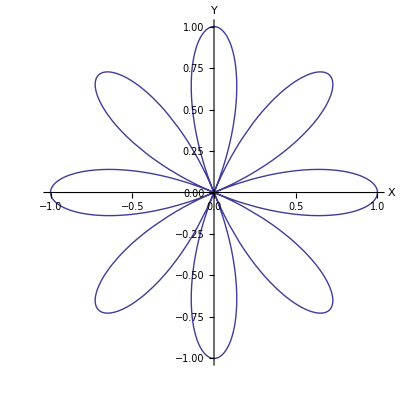

```mathematica
PolarPlot[Cos[4θ],{θ, 0, 2Pi}, AxesLabel -> {"X","Y"}]
```

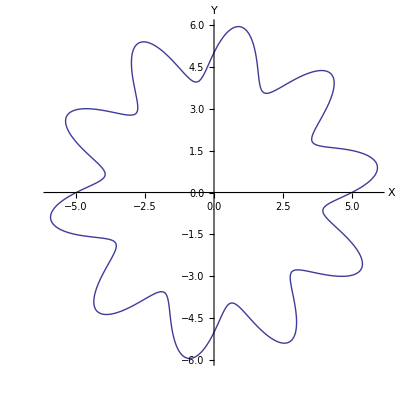

```mathematica
PolarPlot[5+Sin[10θ],{θ,0,2Pi}, AxesLabel -> {"X", "Y"}]
```

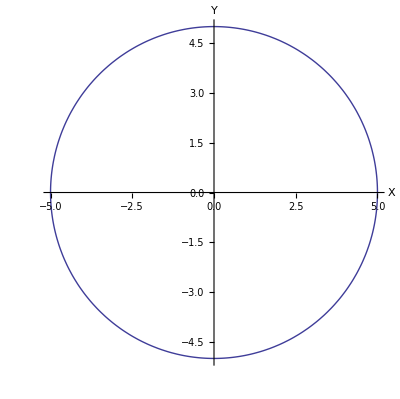

```mathematica
ParametricPlot[{5Cos[θ], 5Sin[θ]},{θ, 0, 2π}, AxesLabel -> {"X", "Y"}]
```

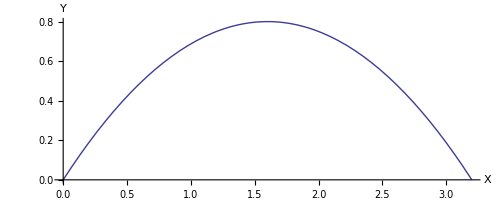

```mathematica
ParametricPlot[{4t, 4t-5t^2},{t, 0, 4/5}, AxesLabel -> {"X", "Y"}]
```

```mathematica
Plot3D[Sin[x*y],{x,0 ,2π},{y,0,2Pi}, Mesh -> False, PlotPoints -> 100]
```

-Graphics3D-

```mathematica
Plot3D[{x^2+y^2,-(x^2+y^2)},{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[x^2-x,{x,0,2}]
```

-Graphics3D-

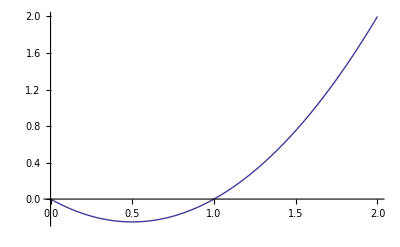

```mathematica
Plot[x^2-x,{x,0,2}]
```

```mathematica
RevolutionPlot3D[{5Cos[θ], 5Sin[θ]},{θ, 0, 2π}, Mesh -> False, PlotPoints -> 150]
```

-Graphics3D-

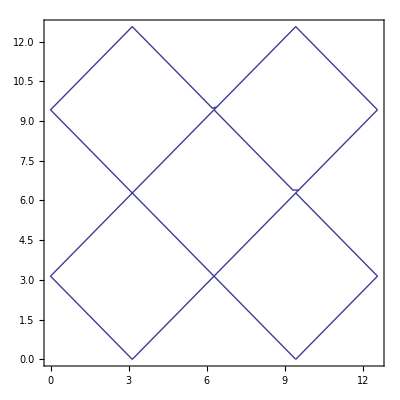

```mathematica
ContourPlot[Cos[x]+Cos[y]==0,{x,0,4Pi},{y,0,4π}]
```

```mathematica
ContourPlot3D[x^2+y^2+z^2,{x,-10,10},{y,-10,10},{z,-10,10}]
```

-Graphics3D-

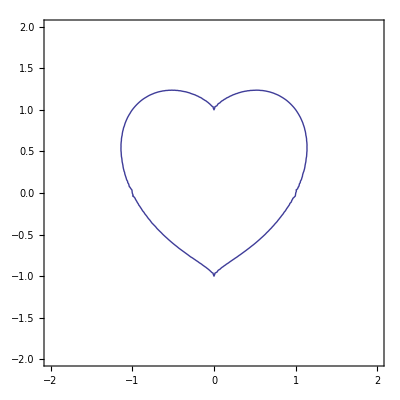

```mathematica
ContourPlot[(x^2+y^2-1)^3-x^2y^3==0,{x,-2,2},{y,-2, 2}]
```

```mathematica
Animate[Plot3D[Sin[x*y*t],{x,0,4Pi},{y,0,4Pi}],{t,0,5}]
```